```mathematica
mychange=genericde/.Idself->1/.Ieself->0/.g->0
```

{dself→(1-m)/n,din→(1-m) (1/(-1+n)-1/((-1+n) n)),dout→m/(-n+d n),eself→0,ein→1/(-1+n),eout→0}

## Large population limit

### BD

```mathematica
lQinM=Limit[QinM/.mychange,d->∞]//FullSimplify
lQoutM=Limit[QoutM/.mychange,d->∞]//FullSimplify
```

(-1+m+μ-m μ)/(-1+m (-1+n) (-1+μ)+μ-n μ)

0

```mathematica
lQinWF=Limit[QinWF/.mychange,d->∞]//FullSimplify
lQoutWF=Limit[QoutWF/.mychange,d->∞]//FullSimplify
```

-((-1+m)^2 (-1+μ)^2)/(-1-2 m (-1+n) (-1+μ)^2+m^2 (-1+n) (-1+μ)^2+(-1+n) (-2+μ) μ)

0

```mathematica
lQM={Qin->lQin, Qout->lQoutM};
lβBDD=Limit[βBDD/.mychange/.lQM,d->∞]//FullSimplify
lβBDI=Limit[βBDI/.mychange/.lQM,d->∞]//FullSimplify
lβBD=Limit[βBD/.mychange/.lQM,d->∞]//FullSimplify
lγBD=Limit[γBD/.mychange/.lQM,d->∞]//FullSimplify
```

lQin-lQin μ

-((-1+m) (1+lQin (-1+n)))/n

-((-1+p) p (-1+m+lQin (1+m (-1+n)-n μ)))/(n μ)

-((-1+p) p (-1+m+lQin (-1+m) (-1+n)+n-n μ))/(n μ)

```mathematica
lβBDD-lβBDI//FullSimplify
Collect[%,lQin,FullSimplify]
```

lQin+((-1+m) (1+lQin (-1+n)))/n-lQin μ

(-1+m)/n+lQin (m+1/n-m/n-μ)

```mathematica
lQin(1-μ)-(-((-1+m) (1+lQin (-1+n)))/n)//FullSimplify
Collect[%,lQin,FullSimplify]

lQin(1-μ)-((1-m) lQin )//FullSimplify
Collect[%,lQin,FullSimplify]
```

(-1+m+lQin (1+m (-1+n)-n μ))/n

(-1+m)/n+(lQin (1+m (-1+n)-n μ))/n

lQin (m-μ)

lQin (m-μ)

```mathematica
(1-m)lQinM//FullSimplify
```

((-1+m)^2 (-1+μ))/(-1+m (-1+n) (-1+μ)+μ-n μ)

((m-μ) (-1+m+μ-m μ))/(-1+m (-1+n) (-1+μ)+μ-n μ)

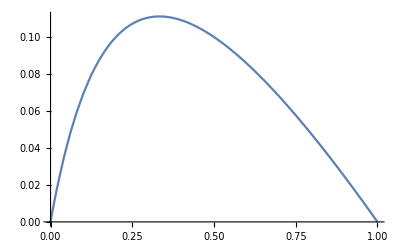

```mathematica
lQin (m-μ)/.lQin->lQinM//FullSimplify
Plot[%/.{μ->0.00,n->4},{m,0,1}]
```

-((-1+m) (-1+p) p (-2+μ))/(-1+m (-1+n) (-1+μ)+μ-n μ)

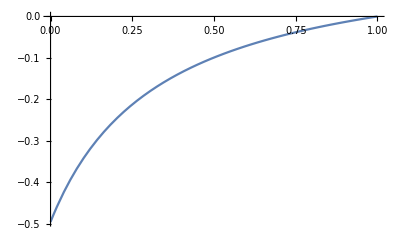

```mathematica
lbBD=lβBD/.lQin->lQinM//FullSimplify
Plot[lβBD/.lQin->lQinM/.{μ->0.00001,n->4,p->0.45},{m,0,1}]
```

```mathematica
D[lbBD,m]//FullSimplify
%/.μ->0
```

(n (-1+p) p (-2+μ))/(-1+m (-1+n) (-1+μ)+μ-n μ)^2

-(2 n (-1+p) p)/(-1-m (-1+n))^2

```mathematica
(-1+m)/n+(lQin (1+m (-1+n)-n μ))/n/.lQin->lQinM//FullSimplify
%/.μ->0
```

((-1+m) (-2+μ) μ)/(-1+m (-1+n) (-1+μ)+μ-n μ)

0

```mathematica
Plot[m lQin/.lQin->lQinM/.{μ->0.0,n->4},{m,0,1}]
```

-Graphics-

```mathematica
tmp=D[b lβBD - c lγBD/.lQM/.lQin->lQinM/.mychange,m]/.m->0//FullSimplify
```

(n (-1+p) p (c+b (-2+μ) μ))/(μ (1+(-1+n) μ)^2)

```mathematica
Limit[tmp,μ->0]//FullSimplify
```

n (-1+p) p DirectedInfinity[c]

```mathematica
D[EXBD/.mychange/.{Idself->1,Ieself->0},m]/.{m->0,p->0.45,n->4,b->15,c->1,d->30,δ->0.005}
```

1/(-29 (-1+μ) μ-116 μ (1+2 μ))0.015 (900 (0.033-9.0495 μ-0.12375 (-1+g) (-2+μ) μ+9.02475 μ^2)+30 (4 (0.04125+1.00275 (-1+μ))-(0.9615-μ) (-1+μ)+0.00275 (15 (2+g (-2+μ)-2 μ)+2 (-1+μ)) μ+μ (1-0.04125 (3+g (-2+μ)-2 μ)-μ-0.00275 (1+2 μ))))-1/(-29 (-1+μ) μ-116 μ (1+2 μ))^2 0.015 ((-1+μ)^2+29 (-1+μ) μ+4 (-1+μ) (1+60 μ)) (0.1155 μ+900 (0.-2.9835 μ+0.12375 (-1+g) (-2+μ) μ-9.02475 μ^2)+30 (-μ (1-0.04125 (3+g (-2+μ)-2 μ)-μ-0.00275 (1+2 μ))+μ (0.0385 μ+16 (0.005 (-0.55+0.55 μ)+μ)+4 (1.00825-2.0055 μ+0.04125 (-3+g (2-μ)+μ)))))

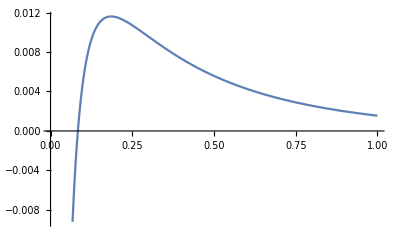

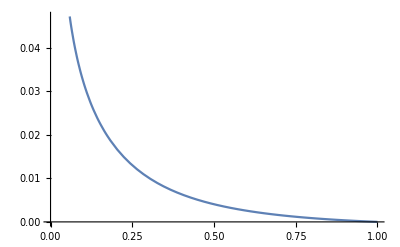

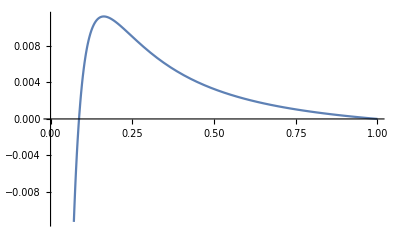

```mathematica
prs={m->0,p->0.45,n->4,b->6,c->1,d->30,δ->0.005};
Plot[D[EXBD/.mychange/.{Idself->1,Ieself->0,g->0},m]/.prs,{μ,0,1}]
Plot[D[EXDB/.mychange/.{Idself->1,Ieself->0,g->0},m]/.prs,{μ,0,1}]
Plot[D[EXWF/.mychange/.{Idself->1,Ieself->0,g->0},m]/.prs,{μ,0,1}]
```

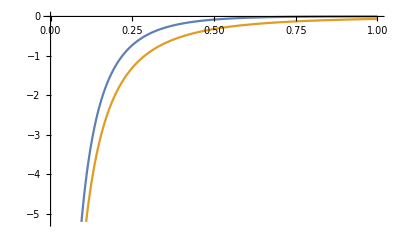

```mathematica
Plot[{D[factorBD βBDD/.{Qin->QinM,Qout->QoutM}/.mychange/.{Idself->1,Ieself->0,g->0},m]/.prs,D[factorBD βBDI/.{Qin->QinM,Qout->QoutM}/.mychange/.{Idself->1,Ieself->0,g->0},m]/.prs},{μ,0,1}]
```

```mathematica
Limit[lβBD/.lQin->lQinM,μ->0]//FullSimplify
Limit[lγBD/.lQin->lQinM,μ->0]//FullSimplify
```

-(2 (-1+m) (-1+p) p)/(1+m (-1+n))

((-1+p) p DirectedInfinity[-(Sign[m] Sign[n]^2)/Sign[1+m (-1+n)]])/n

```mathematica
lβBD-(((1-p) p (-(1-m)+lQin (1-n μ+m (n-1))))/(n μ))//Simplify
```

0

```mathematica
t1=Limit[βBD/.mychange/.{Qin->lQinM,Qout->lQoutM},d->∞]//FullSimplify
t2=Limit[βBD/.mychange/.{Qin->QinM,Qout->QoutM}/.mychange,d->∞]//FullSimplify
t1-t2//Simplify
```

-((-1+m) (-1+p) p (-2+μ))/(-1+m (-1+n) (-1+μ)+μ-n μ)

-((-1+m) (-1+p) p (-2+μ))/(-1+m (-1+n) (-1+μ)+μ-n μ)

0

```mathematica
t1-(-((1-m) (1-p) p (2-μ))/(1+m (n-1) (1-μ)+μ(n-1)))//Simplify
```

0

```mathematica
t3=βBD/.mychange/.{Qin->QinM,Qout->QoutM}/.mychange//FullSimplify
```

-((-1+p) p (μ+d^2 (-1+m) (-2+μ) μ+d (m+(-3+μ) μ)))/(d (-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ)))

```mathematica
t3-(-((1-p) p (μ+d^2 (1-m) (2-μ) μ+d (m+(-3+μ) μ)))/(d(d-1) μ (1+(n-1) μ)+d m (1-μ) (1+d (n-1) μ)))//Simplify
```

0

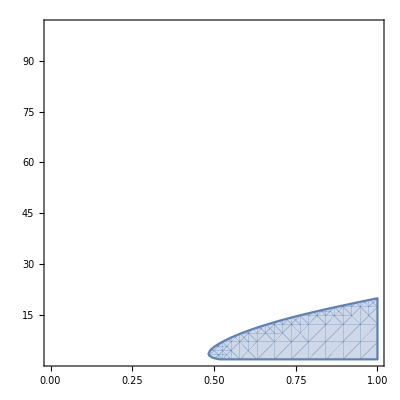

```mathematica
tt3=t3/.{m->0.95,p->0.45,n->2};
RegionPlot[{tt3>0 },{μ,0,1},{d,2,100}]
```

```mathematica
Solve[(d-1)/d==m,d]
%/.m->0.95
```

{{d→1/(1-m)}}

{{d→20.}}

```mathematica
Collect[(μ+d^2 (1-m) (2-μ) μ+d (m+(-3+μ) μ)),m,FullSimplify]
```

-(-1+d) (1+d (-2+μ)) μ+d m (1+d (-2+μ) μ)

```mathematica
Solve[(μ+d^2 (1-m) (2-μ) μ+d (m+(-3+μ) μ))==0,m]//FullSimplify
```

{{m→((-1+d) (1+d (-2+μ)) μ)/(d (1+d (-2+μ) μ))}}

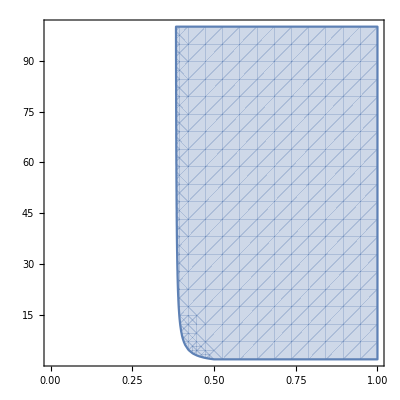

```mathematica
RegionPlot[((-1+d) (1+d (-2+μ)) μ)/(d (1+d (-2+μ) μ))>0 && ((-1+d) (1+d (-2+μ)) μ)/(d (1+d (-2+μ) μ))<1,{μ,0,1},{d,2,100}]
```

```mathematica
Series[lQinM,{m,0,1}]//FullSimplify
```

(-1+μ)/(-1+μ-n μ)+(n (-1+μ) m)/(1+(-1+n) μ)^2+O[m]^2

```mathematica
Series[lbBD,{m,0,1}]//FullSimplify
```

((-1+p) p (-2+μ))/(-1+μ-n μ)+(n (-1+p) p (-2+μ) m)/(1+(-1+n) μ)^2+O[m]^2

```mathematica
Series[lβBDD/.lQin->lQinM,{m,0,1}]//FullSimplify
Series[lβBDI/.lQin->lQinM,{m,0,1}]//FullSimplify
```

(-1+μ)^2/(1+(-1+n) μ)-(n (-1+μ)^2 m)/(1+(-1+n) μ)^2+O[m]^2

1/(1+(-1+n) μ)-(n m)/(1+(-1+n) μ)^2+O[m]^2

### DB

```mathematica
lQM={Qin->lQin, Qout->lQoutM};
lβDBD=Limit[βDBD/.mychange/.lQM,d->∞]//FullSimplify
lβDBI=Limit[βDBI/.mychange/.lQM,d->∞]//FullSimplify
lβDB=Limit[βDB/.mychange/.lQM,d->∞]//FullSimplify
lγDB=Limit[γDB/.mychange/.lQM,d->∞]//FullSimplify
```

lQin-lQin μ

-((-1+m)^2 (1+lQin (-1+n)) (-1+μ))/n

-((-(-1+lQin) (-1+m)^2+lQin (-2+m) m n) (-1+p) p (-1+μ))/(n μ)

-(((-1+m)^2+lQin (-1+m)^2 (-1+n)-n) (-1+p) p (-1+μ))/(n μ)

```mathematica
lbDB=lβDB/.lQin->lQinM//FullSimplify
```

((-1+m) (-1+p) p (m-μ) (-1+μ))/(μ (-1+m (-1+n) (-1+μ)+μ-n μ))

```mathematica
dlbDB=D[lbDB,m]//FullSimplify
dlbDB/.m->0//FullSimplify
```

((-1+p) p (-1+μ) (1+m (-2+m-m n)-μ+((-2+m) m (-1+n)+2 n) μ))/(μ (-1+m (-1+n) (-1+μ)+μ-n μ)^2)

((-1+p) p (-1+μ) (1+(-1+2 n) μ))/(μ (1+(-1+n) μ)^2)

```mathematica
Solve[dlbDB==0,m]//FullSimplify
```

{{m→1+(n (-1+p) (-1+μ)^2)/(n (-1+p) (-1+μ)+√(-n (-1+p)^2 (-1+μ)^2 (-1+(-1+n) (-2+μ) μ)))},{m→1+(n (-1+p) (-1+μ)^2)/(n (-1+p) (-1+μ)-√(-n (-1+p)^2 (-1+μ)^2 (-1+(-1+n) (-2+μ) μ)))}}

```mathematica
mci=1+(n (-1+p) (-1+μ)^2)/(n (-1+p) (-1+μ)+√(-n (-1+p)^2 (-1+μ)^2 (-1+(-1+n) (-2+μ) μ)));
mci/.{n->4,μ->0.001,p->0.45}
```

0.334664

```mathematica
mci/.μ->0//FullSimplify
%/.{n->4,p->0.45}
```

1+(n (-1+p))/(n+√(n (-1+p)^2)-n p)

0.333333

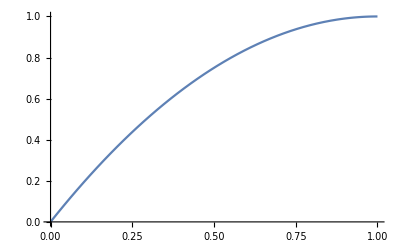

```mathematica
Plot[2m-m^2,{m,0,1}]
```

```mathematica
Limit[lQinM,m->0]//FullSimplify
Limit[%,μ->0]
Limit[lQinM,μ->0]//FullSimplify
```

(-1+μ)/(-1+μ-n μ)

1

(-1+m)/(-1+m-m n)

### WF

```mathematica
lQinWF=Limit[QinWF/.mychange,d->∞]//FullSimplify
lQoutWF=Limit[QoutWF/.mychange,d->∞]//FullSimplify
```

-((-1+m)^2 (-1+μ)^2)/(-1-2 m (-1+n) (-1+μ)^2+m^2 (-1+n) (-1+μ)^2+(-1+n) (-2+μ) μ)

0

```mathematica
lQWF={Qin->lQin, Qout->lQoutWF};
lβWFD=Limit[βWFD/.mychange/.lQWF,d->∞]//FullSimplify
lβWFI=Limit[βWFI/.mychange/.lQWF,d->∞]//FullSimplify
lβWF=Limit[βWF/.mychange/.lQWF,d->∞]//FullSimplify
lγWF=Limit[γWF/.mychange/.lQWF,d->∞]//FullSimplify
```

lQin-lQin μ

-((-1+m)^2 (1+lQin (-1+n)) (-1+μ))/n

-((-(-1+lQin) (-1+m)^2+lQin (-2+m) m n) (-1+p) p (-1+μ))/(n μ)

-(((-1+m)^2+lQin (-1+m)^2 (-1+n)-n) (-1+p) p (-1+μ))/(n μ)

```mathematica
lbWF=lβWF/.lQin->lQinWF//FullSimplify
```

-((-1+m)^2 (-1+p) p (-2+μ) (-1+μ))/(-1-2 m (-1+n) (-1+μ)^2+m^2 (-1+n) (-1+μ)^2+(-1+n) (-2+μ) μ)

```mathematica
dlbWF=D[lbWF,m]//FullSimplify
Solve[dlbWF==0,m]//FullSimplify
```

(2 (-1+m) n (-1+p) p (-2+μ) (-1+μ))/((-1-2 m (-1+n) (-1+μ)^2+m^2 (-1+n) (-1+μ)^2+(-1+n) (-2+μ) μ)^2)

{{m→1}}

```mathematica
dlbWF/.m->0//FullSimplify
```

-(2 n (-1+p) p (-2+μ) (-1+μ))/(-1+(-1+n) (-2+μ) μ)^2

```mathematica
dlbWF/.m->0//FullSimplify
%/.μ->0
```

-(2 n (-1+p) p (-2+μ) (-1+μ))/(-1+(-1+n) (-2+μ) μ)^2

-4 n (-1+p) p

```mathematica
ddlbWF=D[dlbWF,m]//FullSimplify
```

-(2 n (-1+p) p (-2+μ) (-1+μ) (-3 (-1+μ)^2-6 m (-1+n) (-1+μ)^2+3 m^2 (-1+n) (-1+μ)^2+n (4+3 (-2+μ) μ)))/((-1-2 m (-1+n) (-1+μ)^2+m^2 (-1+n) (-1+μ)^2+(-1+n) (-2+μ) μ)^3)

```mathematica
ddlbWF/.m->1//FullSimplify
```

(2 (-1+p) p (-2+μ) (-1+μ))/n

## BD

```mathematica
βBD/.mychange//FullSimplify
```

((-1+p) p ((-1+Qin-n Qin+n Qout) μ-d (-1+Qin+m (1+(-1+n) Qin-n Qout)+n (-Qin+Qout) μ)))/(d n μ)

```mathematica
βBDD/.mychange//FullSimplify
```

Qin-Qin μ

```mathematica
βBDI/.mychange//FullSimplify
```

(-d (-1+m) (1+(-1+n) Qin)+d m n Qout+(-1+Qin-n Qin+n (Qout-d Qout)) μ)/(d n)

```mathematica
tmp=(1-m)((n-1) Qin+1)/n+m  Qout-μ((n-1) Qin+n (d-1)Qout+1)/(n d) ;
tmp-βBDI/.mychange//FullSimplify
```

0

```mathematica
factorBD
```

((1-p) p)/μ

```mathematica
factorBD(βBDD-βBDI)-βBD//FullSimplify
```

0

```mathematica
tmp=βBD/.{Qin->QinM,Qout->QoutM}/.mychange//FullSimplify
```

-((-1+p) p (μ+d^2 (-1+m) (-2+μ) μ+d (m+(-3+μ) μ)))/(d (-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ)))

```mathematica
Limit[tmp,d->∞]//FullSimplify
Limit[%,μ->0]//FullSimplify
```

-((-1+m) (-1+p) p (-2+μ))/(-1+m (-1+n) (-1+μ)+μ-n μ)

-(2 (-1+m) (-1+p) p)/(1+m (-1+n))

```mathematica
tmp=γBD/.{Qin->QinM,Qout->QoutM}/.mychange//FullSimplify
```

((-1+p) p (d m (-1+d n)+(-1+d (3-n+d (-2-2 m (-1+n)+n))) μ+d (1+d (-1+m)) (-1+n) μ^2))/(d (-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ)))

```mathematica
Limit[tmp,μ->0]//FullSimplify
Limit[%,d->∞]//FullSimplify

Limit[tmp,d->∞]//FullSimplify
Limit[%,μ->0]//FullSimplify
```

-(-1+d n) (-1+p) p

n (-1+p) p (-∞)

((-1+p) p (m n+(-2-2 m (-1+n)+n) μ+(-1+m) (-1+n) μ^2))/(μ (-1+m (-1+n) (-1+μ)+μ-n μ))

(-1+p) p DirectedInfinity[Sign[m n]/Sign[-1+m-m n]]

```mathematica
γBD-factorBD(γBDD-γBDI)//FullSimplify
```

0

```mathematica
Normal[Series[tmp,{μ,0,1}]]
```

(1-d n) (-1+p) p+((1-2 d+d^2+d m-d^2 m+d n-2 d^2 n+d^3 n-d^3 m n+d^3 m n^2) (-1+p) p μ)/(d m)

```mathematica
γBDD
```

1-μ

```mathematica
γBDI/.mychange//FullSimplify
```

(-d (-1+m) (1+(-1+n) Qin)+d m n Qout+(-1+Qin-n Qin+n (Qout-d Qout)) μ)/(d n)

```mathematica
Collect[%,μ,FullSimplify]
```

((-1+m) (-1+Qin))/n+Qin-m Qin+m Qout+((-1+Qin-n Qin+n (Qout-d Qout)) μ)/(d n)

```mathematica
Collect[((1-m) (1-Qin))/n+Qin(1-m ),Qin,FullSimplify]
```

(1-m)/n-((-1+m) (-1+n) Qin)/n

```mathematica
γBDI
```

dself+din (-1+n) Qin+dout (-n+d n) Qout-((1+(-1+n) Qin+(-n+d n) Qout) μ)/(d n)

```mathematica
γBDI/.dself->din/.μ->1-noμ
Collect[%,noμ,FullSimplify]
```

din+din (-1+n) Qin+dout (-n+d n) Qout-((1-noμ) (1+(-1+n) Qin+(-n+d n) Qout))/(d n)

(noμ (1+(-1+n) Qin+(-1+d) n Qout))/(d n)+((-1+d din n) (1+(-1+n) Qin)+(-1+d) n (-1+d dout n) Qout)/(d n)

```mathematica
(-1+d din n)/.mychange//FullSimplify
```

-1+d-d m

```mathematica
tmp=(1-m)(1/n+((n-1) Qin)/n)+m Qout-μ(1+(n-1) Qin+n (d-1) Qout)/(d n);
tmp-γBDI/.mychange//FullSimplify
```

0

```mathematica
tmp/.μ->1-noμ//FullSimplify
Collect[%,noμ,FullSimplify]
% - (((d (1-m)-1) (1+(n-1) Qin-n Qout))/(d n)+(noμ (1+(n-1) Qin+(d-1) n Qout))/(d n))//FullSimplify
```

(-(1+d (-1+m)-noμ) (1+(-1+n) Qin)+n (1-noμ+d (-1+m+noμ)) Qout)/(d n)

-((1+d (-1+m)) (1+(-1+n) Qin-n Qout))/(d n)+(noμ (1+(-1+n) Qin+(-1+d) n Qout))/(d n)

0

```mathematica
Qin + Qin μ p p + (1-Qin) μ (1-p)p//FullSimplify
```

Qin+(-1+p) p (-1+Qin) μ+p^2 Qin μ

(1-m) (1/n+((-1+n) Qin)/n)+m Qout

(1-m) (1/n+((-1+n) Qin)/n)+m Qout-(1+(-1+n) Qin+(-1+d) n Qout)/(d n)

((1-m) (1/n+((-1+n) Qin)/n)+m Qout) (1-μ)+((1-m) (1/n+((-1+n) Qin)/n)+m Qout-(1+(-1+n) Qin+(-1+d) n Qout)/(d n)) μ

0

```mathematica
γBDI/.{Qin->QinM,Qout->QoutM}/.mychange//FullSimplify
Limit[factorBD*%,μ->0]
```

(-d m+d (1+d (-1+m)+m) μ+(-1+d-d m) μ^2)/(d (-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ)))

((1-p) p DirectedInfinity[d])/d

```mathematica
tmp=γDB/.{Qin->QinM,Qout->QoutM}/.mychange//FullSimplify
Limit[tmp,μ->0]//FullSimplify
Limit[%,d->∞]//FullSimplify
```

((-1+p) p (-1+μ) (m (2+d (-1+m-n))+(1+d (-1+m)) (-1+n) μ))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))

(2+d (-1+m-n)) (-1+p) p

(-1+m-n) (-1+p) p ∞

```mathematica
Limit[tmp,d->∞]//FullSimplify
Limit[%,μ->0]//FullSimplify
```

((-1+p) p (m n+(-2-2 m (-1+n)+n) μ+(-1+m) (-1+n) μ^2))/(μ (-1+m (-1+n) (-1+μ)+μ-n μ))

(-1+p) p DirectedInfinity[Sign[m n]/Sign[-1+m-m n]]

```mathematica
βBDD-βBDI/.{Qin->QinM,Qout->QoutM}/.mychange//FullSimplify
Sign[%]
```

(μ (μ+d^2 (-1+m) (-2+μ) μ+d (m+(-3+μ) μ)))/(d (-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ)))

Sign[μ (μ+d^2 (-1+m) (-2+μ) μ+d (m+(-3+μ) μ))]/(Sign[d] Sign[-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ)])

```mathematica
Solve[(μ+d^2 (-1+m) (-2+μ) μ+d (m+(-3+μ) μ))==0]//FullSimplify
```

{{m→((-1+d) (1+d (-2+μ)) μ)/(d (1+d (-2+μ) μ))},{d→0,μ→0},{d→1,μ→1}}

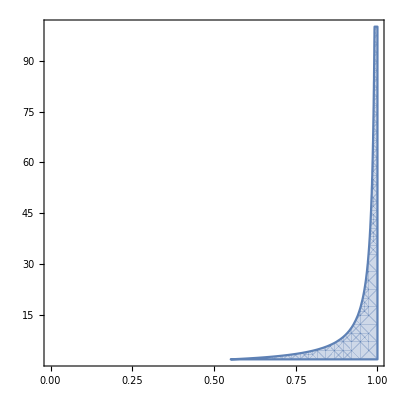

```mathematica
RegionPlot[(μ (μ+d^2 (-1+m) (-2+μ) μ+d (m+(-3+μ) μ)))/(d (-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ)))>0/.{n->4,μ->0.9},{m,0,1},{d,2,100}]
```

```mathematica
NSolve[(d-1)/d==0.9,d]
```

{{d→10.}}

```mathematica
Solve[((-1+d) (1+d (-2+μ)) μ)/(d (1+d (-2+μ) μ))==0]
Solve[((-1+d) (1+d (-2+μ)) μ)/(d (1+d (-2+μ) μ))==1]
```

{{d→1},{μ→0},{μ→(-1+2 d)/d}}

{{d→-μ/(1-3 μ+μ^2)}}

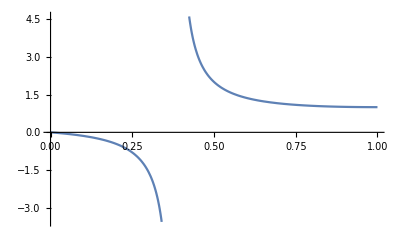

```mathematica
Plot[-μ/(1-3 μ+μ^2),{μ,0,1}]
```

```mathematica
βBDI/.mychange//FullSimplify
```

((1+(-1+n) Qin-n Qout) μ+d (-1+Qin+m (1+(-1+n) Qin-n Qout)+n (-Qin+Qout) μ))/(d n)

(-d (-1+m) (1+(-1+n) Qin)+d m n Qout+(-1+Qin-n Qin+n (Qout-d Qout)) μ)/(d n)

### Derivatives

#### BD

```mathematica
bBD=βBDD-βBDI/.{Qin->QinM,Qout->QoutM}/.mychange//FullSimplify
cBD=γBDD-γBDI/.{Qin->QinM,Qout->QoutM}/.mychange//FullSimplify
combined = b bBD - c cBD
```

(μ (μ+d^2 (-1+m) (-2+μ) μ+d (m+(-3+μ) μ)))/(d (-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ)))

(μ (μ+d (m-d m n+(-3+d (2+2 m (-1+n)-n)+n) μ-(1+d (-1+m)) (-1+n) μ^2)))/(d (-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ)))

(b μ (μ+d^2 (-1+m) (-2+μ) μ+d (m+(-3+μ) μ)))/(d (-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ)))-(c μ (μ+d (m-d m n+(-3+d (2+2 m (-1+n)-n)+n) μ-(1+d (-1+m)) (-1+n) μ^2)))/(d (-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ)))

```mathematica
bBDI=βBDI/.{Qin->QinM,Qout->QoutM}/.mychange//FullSimplify;
D[bBDI,m]//FullSimplify
```

-((-1+d)^2 (1+d n-μ) μ^2)/(d ((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))^2)

```mathematica
db=D[bBD,m]//FullSimplify
dc=D[cBD,m]//FullSimplify
```

-((-1+d)^2 μ^2 (-1+(1+d n (-2+μ)) μ))/(d ((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))^2)

((-1+d)^2 (1+d n-μ) μ^2)/(d ((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))^2)

```mathematica
dcomb=D[combined,m]//FullSimplify
```

-((-1+d)^2 μ^2 (c+c d n-c μ+b (-1+(1+d n (-2+μ)) μ)))/(d ((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))^2)

```mathematica
Solve[dcomb==0]//FullSimplify
sol=Solve[dcomb==0,μ]//FullSimplify
```

{{c→-(b (-1+(1+d n (-2+μ)) μ))/(1+d n-μ)},{d→1},{μ→0},{b→0,n→(-1+μ)/d}}

{{μ→0},{μ→0},{μ→(c+b (-1+2 d n)+√((b-c) (b-c+4 b d^2 n^2)))/(2 b d n)},{μ→-(b-c-2 b d n+√((b-c) (b-c+4 b d^2 n^2)))/(2 b d n)}}

```mathematica
muc=-(b-c-2 b d n+√((b-c) (b-c+4 b d^2 n^2)))/(2 b d n);
muc-(b (2 d n-1)+c-√((b-c) (b-c+4 b d^2 n^2)))/(2 b d n)//Simplify
muc-(1-(b-c+√((b-c) (b-c+4 b d^2 n^2)))/(2 b d n))//Simplify
```

0

0

```mathematica
ex=EXBD/.{Idself->1,Ieself->0,g->0}
dex=D[ex,m]//FullSimplify
```

(p ((b-c) (-1+p) δ μ (m-n+(-1+m) (-1+μ)+μ-m μ)+d^2 (-c m n δ+c m n^2 δ+c m n p δ-c m n^2 p δ+μ-m μ-n μ+2 m n μ-m n^2 μ+2 c δ μ-2 c m δ μ-3 c n δ μ+4 c m n δ μ+c n^2 δ μ-2 c m n^2 δ μ-2 c p δ μ+2 c m p δ μ+3 c n p δ μ-4 c m n p δ μ-c n^2 p δ μ+2 c m n^2 p δ μ-μ^2+m μ^2+2 n μ^2-2 m n μ^2-n^2 μ^2+m n^2 μ^2-c δ μ^2+c m δ μ^2+2 c n δ μ^2-2 c m n δ μ^2-c n^2 δ μ^2+c m n^2 δ μ^2+c p δ μ^2-c m p δ μ^2-2 c n p δ μ^2+2 c m n p δ μ^2+c n^2 p δ μ^2-c m n^2 p δ μ^2-b (-1+p) δ (-(-1+m) (-2+μ) μ+(-1+m) n (-2+μ) μ))+d (m^2 (-1+μ) (-1+c (-1+p) δ+b (δ-p δ)+μ)+m (n (b (δ-p δ)-(-1+c (-1+p) δ) (-1+μ))-(-1+p) δ (b (2-2 μ)+2 c (-1+μ)) μ)+(-1+m) (m (1+b (-1+p) δ+c (δ-p δ)-μ) (-1+μ)+μ (1+b (-1+p) δ (3-2 μ)-μ+c (-1+p) δ (-3+n+2 μ)))+μ ((-b+c) (-1+p) δ μ+n (1+3 c δ-3 c p δ-b (-1+p) δ (-3+μ)-2 μ-2 c δ μ+2 c p δ μ)+n^2 (μ+c δ (-1+p+μ-p μ))))))/(d (m^2 (-1+μ)^2-(-1+m) (-1+μ) (m (-1+μ)+μ-d μ)-(-1+d) n μ (1+(-2+n) μ)+m n (-1+μ) (1+d (-2+n) μ)))

((-1+d)^2 (-1+p) p δ μ (c+c d n-c μ+b (-1+(1+d n (-2+μ)) μ)))/(d ((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))^2)

```mathematica
Solve[dex==0,μ]//FullSimplify
```

{{μ→0},{μ→-(b-c-2 b d n+√((b-c) (b-c+4 b d^2 n^2)))/(2 b d n)},{μ→(c+b (-1+2 d n)+√((b-c) (b-c+4 b d^2 n^2)))/(2 b d n)}}

```mathematica
sol/.{b->2,c->1,d->3000,n->4}//N
```

{{μ→0.},{μ→0.},{μ→1.70709},{μ→0.292872}}

```mathematica
Solve[(-1+(1+NN (-2+μ)) μ)==0,NN]
(-1+(1+d n (-2+μ)) μ)/.{μ->0.1,d->30,n->4}
```

{{NN→(1-μ)/((-2+μ) μ)}}

-23.7

```mathematica
db-dc//FullSimplify
```

-((-1+d)^2 n (-1+μ)^2 μ^2)/((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))^2

```mathematica
db/.m->0//FullSimplify
```

(1-(1+d n (-2+μ)) μ)/(d (1+(-1+n) μ)^2)

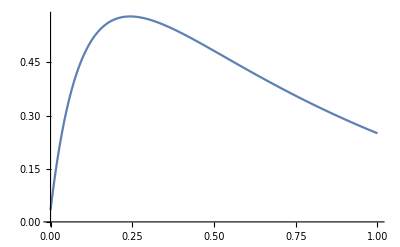

```mathematica
Plot[(1-(1+d n (-2+μ)) μ)/(d (1+(-1+n) μ)^2)/.{d->30,n->4},{μ,0,1}]
```

```mathematica
factorBD
```

((1-p) p)/μ

```mathematica
D[factorBD(b bBD-c cBD),m]//FullSimplify
```

((-1+d)^2 (-1+p) p μ (c+c d n-c μ+b (-1+(1+d n (-2+μ)) μ)))/(d ((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))^2)

```mathematica
((-1+d)^2 (-1+p) p μ (c+c d n-c μ+b (-1+(1+d n (-2+μ)) μ)))/(d ((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))^2)/.{d->30,n->4,b->15,c->1,p->0.45}/.μ->0.2
```

748.221/(9.28+15.2 m)^2

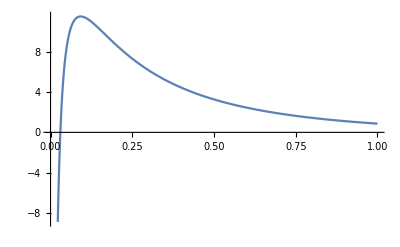

```mathematica
Plot[((-1+d)^2 (-1+p) p μ (c+c d n-c μ+b (-1+(1+d n (-2+μ)) μ)))/(d ((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))^2)/.{d->30,n->4,b->15,c->1,p->0.45,m->0},{μ,0,1}]
```

## DB

```mathematica
βDBI/.{dself->din,eself->0,eout->0,ein->1/(n-1)}//FullSimplify
Collect[%,μ,FullSimplify]
```

-n ((din^2+(-1+d) dout^2) (1+(-1+n) Qin)+(-1+d) dout (2 din+(-2+d) dout) n Qout) (-1+μ)

n ((din^2+(-1+d) dout^2) (1+(-1+n) Qin)+(-1+d) dout (2 din+(-2+d) dout) n Qout)-n ((din^2+(-1+d) dout^2) (1+(-1+n) Qin)+(-1+d) dout (2 din+(-2+d) dout) n Qout) μ

```mathematica
factorDB(βDBD-βDBI)-βDB//FullSimplify
```

-βDB+factorDB (βDBD-βDBI)

```mathematica
βDBD/.mychange//FullSimplify
```

Qin-Qin μ

```mathematica
dout/.mychange
```

m/(-n+d n)

```mathematica
din/.mychange//FullSimplify
dout/.mychange//FullSimplify
```

(1-m)/n

m/((-1+d) n)

```mathematica
t2=(1-μ)((1+(n-1)Qin)((1-m)^2/n+m^2/(n(d-1)))+m(2(1-m)+(d-2)m/(d-1))Qout)
```

(((1-m)^2/n+m^2/((-1+d) n)) (1+(-1+n) Qin)+m (2 (1-m)+((-2+d) m)/(-1+d)) Qout) (1-μ)

```mathematica
t2-tt/.mychange//FullSimplify
```

0

```mathematica
tt=n ((din^2+(d-1) dout^2) (1+(n-1) Qin)+(d-1) dout (2 din+(d-2) dout) n Qout) (1-μ);
tt/.mychange
```

```mathematica
tt-βDBI/.{dself->din,eself->0,eout->0,ein->1/(n-1)}//FullSimplify
```

n (((1-m)^2 (1/(-1+n)-1/((-1+n) n))^2+((-1+d) m^2)/(-n+d n)^2) (1+(-1+n) Qin)+((-1+d) m n (2 (1-m) (1/(-1+n)-1/((-1+n) n))+((-2+d) m)/(-n+d n)) Qout)/(-n+d n)) (1-μ)

0

```mathematica
ttt=βDBI/.mychange//FullSimplify
Collect[%,μ,FullSimplify]
```

-(((-1+d (-1+m)^2+2 m) (1+(-1+n) Qin)-(2+d (-2+m)) m n Qout) (-1+μ))/((-1+d) n)

((-1+d (-1+m)^2+2 m) (1+(-1+n) Qin)-(2+d (-2+m)) m n Qout)/((-1+d) n)-(((-1+d (-1+m)^2+2 m) (1+(-1+n) Qin)-(2+d (-2+m)) m n Qout) μ)/((-1+d) n)

```mathematica
-(2+d (-2+m))-(-2+2d-d m)//Simplify
```

0

```mathematica
tmp0=ttt/.μ->0
tmp1=ttt/.μ->1
(μ tmp1 + (1-μ)tmp0)
ttt-%//FullSimplify
```

((-1+d (-1+m)^2+2 m) (1+(-1+n) Qin)-(2+d (-2+m)) m n Qout)/((-1+d) n)

0

(((-1+d (-1+m)^2+2 m) (1+(-1+n) Qin)-(2+d (-2+m)) m n Qout) (1-μ))/((-1+d) n)

0

```mathematica
ttt/.{Qout->0}//FullSimplify
((d-1 -2m (d-1) + d m^2) (1+(n-1) Qin) (1-μ))/(n(d-1))-%//FullSimplify
```

-((-1+d (-1+m)^2+2 m) (1+(-1+n) Qin) (-1+μ))/((-1+d) n)

0

```mathematica
Collect[((-1+d (-1+m)^2+2 m) (1+(-1+n) Qin)-(2+d (-2+m)) m n Qout)/((-1+d) n),Qin]
Collect[((-1+d (-1+m)^2+2 m) (1+(-1+n) Qin)-(2+d (-2+m)) m n Qout)/((-1+d) n),Qout]
```

((-1+d (-1+m)^2+2 m) (-1+n) Qin)/((-1+d) n)+(-1+d (-1+m)^2+2 m-(2+d (-2+m)) m n Qout)/((-1+d) n)

((-1+d (-1+m)^2+2 m) (1+(-1+n) Qin))/((-1+d) n)+((-2-d (-2+m)) m Qout)/(-1+d)

```mathematica
γDBI/.{dself->din,eself->0,eout->0,ein->1/(n-1)}//FullSimplify
```

n ((din^2+(-1+d) dout^2) (1+(-1+n) Qin)+(-1+d) dout (2 din+(-2+d) dout) n Qout) (1-μ)

```mathematica
γDBI-βDBI/.{eself->0,eout->0,ein->1/(n-1)}//FullSimplify
```

(din-dself)^2 (-1+Qin) (-1+μ)

```mathematica
βWFI-βDBI
γWFI-γDBI
```

0

0

```mathematica
γBDD
γDBD
γWFD
```

1-μ

1-μ

1-μ

### Derivatives

```mathematica
bDBI=βDBI/.{Qin->QinM,Qout->QoutM}/.mychange//FullSimplify
bDB=βDBD-βDBI/.{Qin->QinM,Qout->QoutM}/.mychange//FullSimplify
cDB=γDBD-γDBI/.{Qin->QinM,Qout->QoutM}/.mychange//FullSimplify
combined = b bDB - c cDB//FullSimplify
```

((-1+μ) (m+(1+d (-1+m)) (-1+m) μ))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))

((-1+μ) μ (m (-2+d-d m)+μ+d (-1+m) μ))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))

-((-1+μ) μ (m (2+d (-1+m-n))+(1+d (-1+m)) (-1+n) μ))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))

((-1+μ) μ (-(b-c) (2+d (-1+m)) m-c d m n+(1+d (-1+m)) (b+c (-1+n)) μ))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))

```mathematica
ex=EXDB/.{Idself->1,Ieself->0,g->0}//FullSimplify
```

(p ((b-c) d m^2 (-1+p) δ (-1+μ)+(-1+d) μ (-1+b (-1+p) δ (-1+μ)+c (-1+n) (-1+p) δ (-1+μ)+μ-n μ)-m (-1+μ) (-1+d μ-d n μ+b (-1+p) δ (-2+d+d μ)+c (-1+p) δ (2-d (1+n)+d (-1+n) μ))))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))

```mathematica
dbi=D[bDBI,m]//FullSimplify
db=D[bDB,m]//FullSimplify
dc=D[cDB,m]//FullSimplify
```

((-1+μ) (-(-1+μ) (m+(1+d (-1+m)) (-1+m) μ) (1+d (-1+n) μ)+(1+(1+2 d (-1+m)) μ) (-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))))/((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))^2

-((-1+μ) μ (-d m^2+μ+d (-2+m (2+m)+d (1+m (-2+m-m n))) μ+(-(1+d (-1+m))^2+(2+2 d (-2+m)+d^2 (2+(-2+m) m)) n) μ^2))/((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))^2

-((-1+μ) μ (-d m^2+μ+(n+d (m (2+m)-2 (1+n)-d (-1+m) (1+m (-1+n)+n))) μ+(1+d (-1+m))^2 (-1+n) μ^2))/((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))^2

```mathematica
Solve[dbi==0]//FullSimplify
sol=Solve[dbi==0,m]//FullSimplify
```

{{n→((-1+μ) (-d m^2+(1+d (-1+m))^2 μ))/((1+d (-1+m)) μ (1-d (1+m)+μ+d (-1+m) μ))},{μ→0},{μ→1},{d→(1+μ)^2/(4 μ),m→(-1+μ)/(1+μ)},{d→0,μ→0},{m→(-1+d)/d,μ→1}}

{{m→((-1+d) d (-1+μ) μ (1+(-1+n) μ)-√((-1+d)^2 d (-1+μ)^2 μ (n+(-1+μ)^2+d n^2 μ-n μ^2)))/(d (-1+μ)^2 (1+d (-1+n) μ))},{m→((-1+d) d (-1+μ) μ (1+(-1+n) μ)+√((-1+d)^2 d (-1+μ)^2 μ (n+(-1+μ)^2+d n^2 μ-n μ^2)))/(d (-1+μ)^2 (1+d (-1+n) μ))}}

```mathematica
sol/.{d->40,μ->0.01,n->4}
```

{{m→-1.13952},{m→0.77065}}

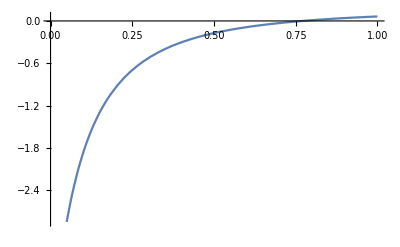

```mathematica
Plot[dbi/.{d->40,μ->0.01,n->4},{m,0,1}]
```

```mathematica
mcc=((-1+d) d (-1+μ) μ (1+(-1+n) μ)+√((-1+d)^2 d (-1+μ)^2 μ (n+(-1+μ)^2+d n^2 μ-n μ^2)))/(d (-1+μ)^2 (1+d (-1+n) μ));
```

```mathematica
dmc=mcc-mc//FullSimplify
Solve[%==0,d]
dmc/.{d->30,n->4,μ->0.2}
```

(1+(√((-1+d)^2 d (-1+μ)^2 μ (n+(-1+μ)^2+d n^2 μ-n μ^2))+d (-1+μ) (1+μ (-2+d n+μ-n μ)))/((-1+μ)^2 (1+d (-1+n) μ)))/d

{{d→1}}

-0.0156692

#### Combined

```mathematica
Limit[ex,μ->0]//FullSimplify
D[%,m]//FullSimplify
```

p (1+((b-c) (2+d (-1+m))+c d n) (-1+p) δ)

(b-c) d (-1+p) p δ

```mathematica
Limit[combined,m->0]
D[%,μ]/.μ->0
```

((b+c (-1+n)) (-1+μ) μ)/(1+(-1+n) μ)

-b-c (-1+n)

```mathematica
D[combined,μ]/.μ->0;
Collect[%,{b,c},FullSimplify]
```

0

b (-2+d-d m)+c (2+d (-1+m-n))

Derivative with respect to m

```mathematica
dcb=D[combined,m]//FullSimplify
```

((-1+μ) μ (-(-1+μ) (-(b-c) (2+d (-1+m)) m-c d m n+(1+d (-1+m)) (b+c (-1+n)) μ) (1+d (-1+n) μ)+(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ)) (b (-2+d (1-2 m+μ))+c (2+d (-1+2 m-n+(-1+n) μ)))))/((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))^2

```mathematica
dcb0=Limit[dcb,m->0]//FullSimplify
```

((-1+μ) (c (1+n+(-1+n) μ)+b (-1+μ-2 n μ)))/(1+(-1+n) μ)^2

```mathematica
dcb0-((1-μ) (-c (1+n+(n-1) μ)+b (1-μ+2 n μ)))/(1+(-1+n) μ)^2//Simplify
```

0

```mathematica
Solve[dcb0==0,μ]//FullSimplify
muc0DB=μ/.%⟦2⟧
```

{{μ→1},{μ→(-b+c+c n)/(c-c n+b (-1+2 n))}}

(-b+c+c n)/(c-c n+b (-1+2 n))

```mathematica
muc0DB-(b-c (n+1))/(c (n-1)-b (2 n-1))//Simplify
```

0

```mathematica
Solve[muc0DB==0,b]
```

{{b→c (1+n)}}

```mathematica
Limit[dcb,m->∞]//FullSimplify
```

((-b+c) d μ)/(1+d (-1+n) μ)

```mathematica
dcb1=dcb/.m->1//FullSimplify
```

-((-1+μ) μ (b (-d+μ+d (1-d n) μ+(-1+(2+(-2+d) d) n) μ^2)+c (d+d (-1+2 n) μ-μ (1+n+(-1+n) μ))))/(-1+μ (2-d n+(-1+n) μ))^2

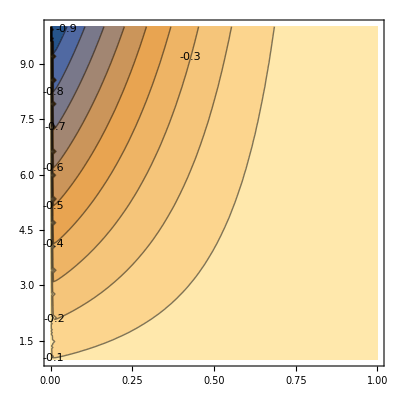

```mathematica
ContourPlot[dcb1/.{d->1000,n->10,c->1},{μ,0,1},{b,1,10},ContourLabels->All]
```

```mathematica
muc0DB/.{n->4,b->7,c->1}//N
```

-0.0434783

When does it vanish? and what is its sign?

```mathematica
solmDB=Solve[dcb==0,m]//FullSimplify
```

{{m→((b-c) (-1+d) d (-1+μ) μ (1+(-1+n) μ)+√(-(b-c) (-1+d)^2 d (-1+μ)^2 μ (c (1+n)+c μ (-2+d n^2+μ-n μ)+b (-1+μ (2-μ+n (2 (-1+μ)+d (-1+(-1+n) (-2+μ) μ)))))))/((b-c) d (-1+μ)^2 (1+d (-1+n) μ))},{m→((b-c) (-1+d) d (-1+μ) μ (1+(-1+n) μ)-√(-(b-c) (-1+d)^2 d (-1+μ)^2 μ (c (1+n)+c μ (-2+d n^2+μ-n μ)+b (-1+μ (2-μ+n (2 (-1+μ)+d (-1+(-1+n) (-2+μ) μ)))))))/((b-c) d (-1+μ)^2 (1+d (-1+n) μ))}}

```mathematica
mcDB=m/.solmDB⟦2⟧;
Limit[mcDB,μ->0]
```

0

```mathematica
Limit[mcDB,d->∞]
Limit[%,μ->0]//FullSimplify

Limit[mcDB,μ->0]
Limit[%,d->∞]//FullSimplify
```

((b-c) (-1+μ) μ (1+(-1+n) μ)-√((b-c) n (-1+μ)^2 μ^2 (-c n-b (-1+(-1+n) (-2+μ) μ))))/((b-c) (-1+n) (-1+μ)^2 μ)

-(b-c+√((b-c) n (b-c n)))/((b-c) (-1+n))

0

0

Find the admissible solution

{{m→-0.158799+0.332271 ⅈ},{m→-0.158799-0.332271 ⅈ}}

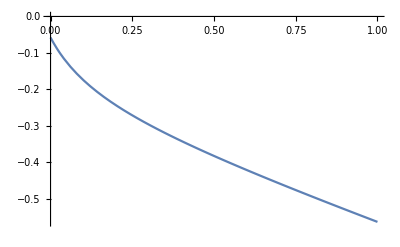

{{m→-0.0823621},{m→-0.235235}}

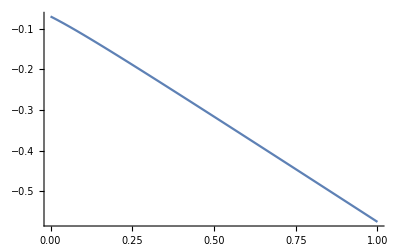

{{m→0.0339181},{m→-0.351515}}

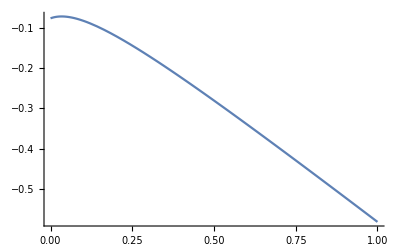

```mathematica
prms={b->3,c->1,μ->0.01,d->30,n->4};
solmDB/.prms
Plot[combined/.prms,{m,0,1},AxesOrigin->{0,0}]
prms={b->4.3,c->1,μ->0.01,d->30,n->4};
solmDB/.prms
Plot[combined/.prms,{m,0,1},AxesOrigin->{0,0},PlotRange->All]

prms={b->5,c->1,μ->0.01,d->30,n->4};
solmDB/.prms
Plot[combined/.prms,{m,0,1},AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
mcDB/.b->c(n-1)//FullSimplify
```

(c (-1+d) d (-2+n) (-1+μ) μ (1+(-1+n) μ)-√(-c^2 (-1+d)^2 d (-2+n) (-1+μ)^2 μ (2+(-4+(4+d-2 n) n) μ-2 (-1+n)^2 (-1+d n) μ^2+d (-1+n)^2 n μ^3)))/(c d (-2+n) (-1+μ)^2 (1+d (-1+n) μ))

```mathematica
D[dcb,m]//FullSimplify
```

(2 (-1+d)^2 (-1+μ) μ^2 (c (1+n)+c μ (-2+d n^2+μ-n μ)+b (-1+μ (2-μ+n (2 (-1+μ)+d (-1+(-1+n) (-2+μ) μ))))))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))^3

```mathematica
sqrtm=-(b-c) (-1+d)^2 d (-1+μ)^2 μ (c (1+n)+c μ (-2+d n^2+μ-n μ)+b (-1+μ (2-μ+n (2 (-1+μ)+d (-1+(-1+n) (-2+μ) μ)))));
```

```mathematica
Solve[sqrtm==0,b]//FullSimplify
%/.prms
```

{{b→c},{b→-(c (n+(-1+μ)^2+d n^2 μ-n μ^2))/(-1+μ (2-μ+n (2 (-1+μ)+d (-1+(-1+n) (-2+μ) μ))))}}

{{5→1},{5→4.1956}}

```mathematica
solmuDB=Solve[dcb==0,μ]
```

{{μ→0},{μ→1},{μ→(-b+c+2 b d-2 c d-b d^2+c d^2-2 b d m+2 c d m+2 b d^2 m-2 c d^2 m-b d m^2+c d m^2-b d^2 m^2+c d^2 m^2+c n-2 c d n+c d^2 n+b d^2 m^2 n-c d^2 m^2 n-√(-4 (-b d m^2+c d m^2) (-b+c+2 b d-2 c d-b d^2+c d^2-2 b d m+2 c d m+2 b d^2 m-2 c d^2 m-b d^2 m^2+c d^2 m^2+2 b n-c n-4 b d n+2 c d n+2 b d^2 n-c d^2 n+2 b d m n-2 c d m n-2 b d^2 m n+2 c d^2 m n+b d^2 m^2 n-c d^2 m^2 n)+(b-c-2 b d+2 c d+b d^2-c d^2+2 b d m-2 c d m-2 b d^2 m+2 c d^2 m+b d m^2-c d m^2+b d^2 m^2-c d^2 m^2-c n+2 c d n-c d^2 n-b d^2 m^2 n+c d^2 m^2 n)^2))/(2 (-b+c+2 b d-2 c d-b d^2+c d^2-2 b d m+2 c d m+2 b d^2 m-2 c d^2 m-b d^2 m^2+c d^2 m^2+2 b n-c n-4 b d n+2 c d n+2 b d^2 n-c d^2 n+2 b d m n-2 c d m n-2 b d^2 m n+2 c d^2 m n+b d^2 m^2 n-c d^2 m^2 n))},{μ→(-b+c+2 b d-2 c d-b d^2+c d^2-2 b d m+2 c d m+2 b d^2 m-2 c d^2 m-b d m^2+c d m^2-b d^2 m^2+c d^2 m^2+c n-2 c d n+c d^2 n+b d^2 m^2 n-c d^2 m^2 n+√(-4 (-b d m^2+c d m^2) (-b+c+2 b d-2 c d-b d^2+c d^2-2 b d m+2 c d m+2 b d^2 m-2 c d^2 m-b d^2 m^2+c d^2 m^2+2 b n-c n-4 b d n+2 c d n+2 b d^2 n-c d^2 n+2 b d m n-2 c d m n-2 b d^2 m n+2 c d^2 m n+b d^2 m^2 n-c d^2 m^2 n)+(b-c-2 b d+2 c d+b d^2-c d^2+2 b d m-2 c d m-2 b d^2 m+2 c d^2 m+b d m^2-c d m^2+b d^2 m^2-c d^2 m^2-c n+2 c d n-c d^2 n-b d^2 m^2 n+c d^2 m^2 n)^2))/(2 (-b+c+2 b d-2 c d-b d^2+c d^2-2 b d m+2 c d m+2 b d^2 m-2 c d^2 m-b d^2 m^2+c d^2 m^2+2 b n-c n-4 b d n+2 c d n+2 b d^2 n-c d^2 n+2 b d m n-2 c d m n-2 b d^2 m n+2 c d^2 m n+b d^2 m^2 n-c d^2 m^2 n))}}

```mathematica
solmuDB/.{b->4,c->1,m->0.1,d->30,n->4}
```

{{μ→0},{μ→1},{μ→-0.000618478},{μ→0.0744721}}

```mathematica
mucDB=(-b+c+2 b d-2 c d-b d^2+c d^2-2 b d m+2 c d m+2 b d^2 m-2 c d^2 m-b d m^2+c d m^2-b d^2 m^2+c d^2 m^2+c n-2 c d n+c d^2 n+b d^2 m^2 n-c d^2 m^2 n+√(-4 (-b d m^2+c d m^2) (-b+c+2 b d-2 c d-b d^2+c d^2-2 b d m+2 c d m+2 b d^2 m-2 c d^2 m-b d^2 m^2+c d^2 m^2+2 b n-c n-4 b d n+2 c d n+2 b d^2 n-c d^2 n+2 b d m n-2 c d m n-2 b d^2 m n+2 c d^2 m n+b d^2 m^2 n-c d^2 m^2 n)+(b-c-2 b d+2 c d+b d^2-c d^2+2 b d m-2 c d m-2 b d^2 m+2 c d^2 m+b d m^2-c d m^2+b d^2 m^2-c d^2 m^2-c n+2 c d n-c d^2 n-b d^2 m^2 n+c d^2 m^2 n)^2))/(2 (-b+c+2 b d-2 c d-b d^2+c d^2-2 b d m+2 c d m+2 b d^2 m-2 c d^2 m-b d^2 m^2+c d^2 m^2+2 b n-c n-4 b d n+2 c d n+2 b d^2 n-c d^2 n+2 b d m n-2 c d m n-2 b d^2 m n+2 c d^2 m n+b d^2 m^2 n-c d^2 m^2 n))
```

(-b+c+2 b d-2 c d-b d^2+c d^2-2 b d m+2 c d m+2 b d^2 m-2 c d^2 m-b d m^2+c d m^2-b d^2 m^2+c d^2 m^2+c n-2 c d n+c d^2 n+b d^2 m^2 n-c d^2 m^2 n+√(-4 (-b d m^2+c d m^2) (-b+c+2 b d-2 c d-b d^2+c d^2-2 b d m+2 c d m+2 b d^2 m-2 c d^2 m-b d^2 m^2+c d^2 m^2+2 b n-c n-4 b d n+2 c d n+2 b d^2 n-c d^2 n+2 b d m n-2 c d m n-2 b d^2 m n+2 c d^2 m n+b d^2 m^2 n-c d^2 m^2 n)+(b-c-2 b d+2 c d+b d^2-c d^2+2 b d m-2 c d m-2 b d^2 m+2 c d^2 m+b d m^2-c d m^2+b d^2 m^2-c d^2 m^2-c n+2 c d n-c d^2 n-b d^2 m^2 n+c d^2 m^2 n)^2))/(2 (-b+c+2 b d-2 c d-b d^2+c d^2-2 b d m+2 c d m+2 b d^2 m-2 c d^2 m-b d^2 m^2+c d^2 m^2+2 b n-c n-4 b d n+2 c d n+2 b d^2 n-c d^2 n+2 b d m n-2 c d m n-2 b d^2 m n+2 c d^2 m n+b d^2 m^2 n-c d^2 m^2 n))

```mathematica
mucDB
```

```mathematica
sol=Solve[dcb==0,b]//FullSimplify
```

{{b→(c (-d m^2+(1+n+d (m (2+m)-2 (1+n)-d (-1+m) (1+m (-1+n)+n))) μ+(1+d (-1+m))^2 (-1+n) μ^2))/(-d m^2+μ+d (-2+m (2+m)+d (1+m (-2+m-m n))) μ+(-(1+d (-1+m))^2+(2+2 d (-2+m)+d^2 (2+(-2+m) m)) n) μ^2)}}

```mathematica
sol=Solve[dcb==0,m]//FullSimplify
```

{{m→((b-c) (-1+d) d (-1+μ) μ (1+(-1+n) μ)+√(-(b-c) (-1+d)^2 d (-1+μ)^2 μ (c (1+n)+c μ (-2+d n^2+μ-n μ)+b (-1+μ (2-μ+n (2 (-1+μ)+d (-1+(-1+n) (-2+μ) μ)))))))/((b-c) d (-1+μ)^2 (1+d (-1+n) μ))},{m→((b-c) (-1+d) d (-1+μ) μ (1+(-1+n) μ)-√(-(b-c) (-1+d)^2 d (-1+μ)^2 μ (c (1+n)+c μ (-2+d n^2+μ-n μ)+b (-1+μ (2-μ+n (2 (-1+μ)+d (-1+(-1+n) (-2+μ) μ)))))))/((b-c) d (-1+μ)^2 (1+d (-1+n) μ))}}

```mathematica
sol/.{b->10,c->1,μ->0.2,n->4,d->30}
```

{{m→0.451008},{m→-1.67206}}

```mathematica
mcDB=((b-c) (-1+d) d (-1+μ) μ (1+(-1+n) μ)+√(-(b-c) (-1+d)^2 d (-1+μ)^2 μ (c (1+n)+c μ (-2+d n^2+μ-n μ)+b (-1+μ (2-μ+n (2 (-1+μ)+d (-1+(-1+n) (-2+μ) μ)))))))/((b-c) d (-1+μ)^2 (1+d (-1+n) μ))//FullSimplify;
```

```mathematica
mcDB
```

((b-c) (-1+d) d (-1+μ) μ (1+(-1+n) μ)+√((-b+c) (-1+d)^2 d (-1+μ)^2 μ (c (1+n)+c μ (-2+d n^2+μ-n μ)+b (-1+μ (2-μ+n (2 (-1+μ)+d (-1+(-1+n) (-2+μ) μ)))))))/((b-c) d (-1+μ)^2 (1+d (-1+n) μ))

```mathematica
Limit[mcDB,μ->0]
```

0

```mathematica
Solve[mcDB==0,μ]
```

$Aborted

```mathematica
Limit[dcb,m->0]//FullSimplify
Solve[%==0,b]//FullSimplify
```

((-1+μ) (c (1+n+(-1+n) μ)+b (-1+μ-2 n μ)))/(1+(-1+n) μ)^2

{{b→(c (1+n+(-1+n) μ))/(1+(-1+2 n) μ)}}

```mathematica
bc=(c (1+n+(-1+n) μ))/(1+(-1+2 n) μ);
```

```mathematica
Limit[bc,μ->0]
```

c (1+n)

```mathematica
mcDB/.b->(c (1+n+(-1+n) μ))/(1+(-1+2 n) μ)//FullSimplify
```

(c (-1+d) d n (-1+μ)^2 μ (1+(-1+n) μ)+√((c^2 (-1+d)^2 d^2 n^2 (-1+μ)^4 μ^2 (1+(-1+n) μ)^2)/(-1+μ-2 n μ)^2) (-1+μ-2 n μ))/(c d n (-1+μ)^3 (1+d (-1+n) μ))

```mathematica
ddcb=D[dcb,m]//FullSimplify
```

(2 (-1+d)^2 (-1+μ) μ^2 (c (1+n)+c μ (-2+d n^2+μ-n μ)+b (-1+μ (2-μ+n (2 (-1+μ)+d (-1+(-1+n) (-2+μ) μ))))))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))^3

```mathematica
Solve[ddcb==0,b]//FullSimplify
```

{{b→-(c (n+(-1+μ)^2+d n^2 μ-n μ^2))/(-1+μ (2-μ+n (2 (-1+μ)+d (-1+(-1+n) (-2+μ) μ))))}}

```mathematica
bcc=-(c (n+(-1+μ)^2+d n^2 μ-n μ^2))/(-1+μ (2-μ+n (2 (-1+μ)+d (-1+(-1+n) (-2+μ) μ))));
```

```mathematica
Limit[mcDB,μ->0]
```

0

```mathematica
Solve[mcDB==0,b]
```

$Aborted

```mathematica
{bc,bcc}/.{c->1,μ->0.001,n->4,d->1000}
```

{4.96822,4.17457}

```mathematica
bc-bcc//FullSimplify
Solve[%==0,μ]
```

(c d n (-1+μ) μ (1+(-1+n) μ)^2)/((1+(-1+2 n) μ) (-1+μ (2-μ+n (2 (-1+μ)+d (-1+(-1+n) (-2+μ) μ)))))

{{μ→0},{μ→1},{μ→1/(1-n)},{μ→1/(1-n)}}

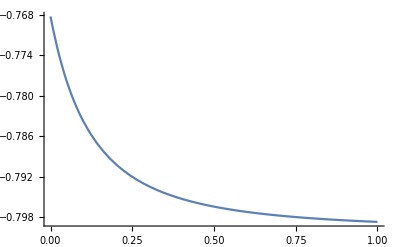

```mathematica
Plot[dcb/.{b->4.2,c->1,μ->0.001,n->4,d->1000},{m,0,1},AxesOrigin->{0,0},PlotRange->All]
```

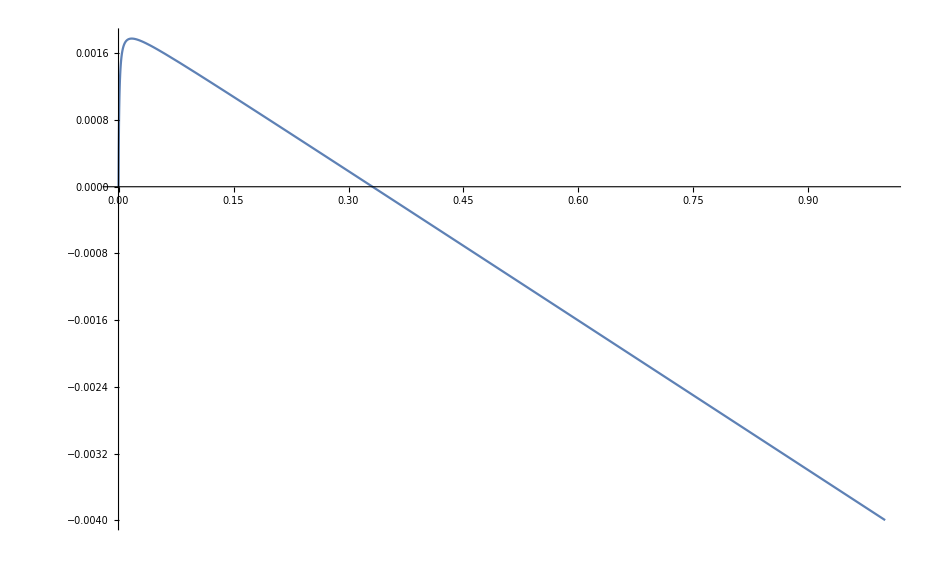

```mathematica
Plot[combined/.{b->7,c->1,μ->0.000001,n->4,d->1000},{m,0,1},AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
exdb=EXDB/.{Qin->QinM,Qout->QoutM}/.mychange/.{Idself->1,Ieself->0,g->0}
```

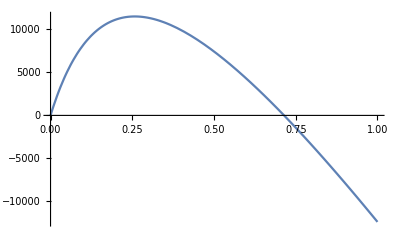

```mathematica
Plot[exdb/.{b->15,c->1,n->4,d->30000000000,δ->0.005,p->0.45,μ->0.0000001},{m,0,1}]
```

```mathematica
Solve[combined==0,b]//FullSimplify
bcpos=b/.%⟦1⟧
```

{{b→(c m (2+d (-1+m-n))+c (1+d (-1+m)) (-1+n) μ)/((2+d (-1+m)) m+(-1+d-d m) μ)}}

(c m (2+d (-1+m-n))+c (1+d (-1+m)) (-1+n) μ)/((2+d (-1+m)) m+(-1+d-d m) μ)

```mathematica
bcpos/.{c->1,μ->0.001,n->4,d->1000,m->0.01}
```

5.94388

```mathematica
dbb=bc-bcpos//FullSimplify
Solve[%==0,d]
```

c (-1+n-((2+d (-2+m)) m n)/((2+d (-1+m)) m+(-1+d-d m) μ)+(1+n+(-1+n) μ)/(1+(-1+2 n) μ))

{{d→-(2 (-m+μ+m μ-μ^2+n μ^2))/(-m^2-2 μ+2 m μ+m^2 μ-2 m n μ+2 μ^2-2 m μ^2-2 n μ^2+2 m n μ^2)}}

```mathematica
Limit[dbb,m->0]//FullSimplify
```

(2 c n (1+(-1+n) μ))/(1+(-1+2 n) μ)

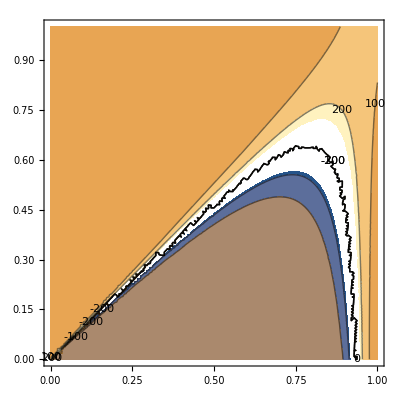

```mathematica
ContourPlot[dbb/.{n->4,c->1},{m,0,1},{μ,0,1},ContourLabels->True]
```

```mathematica
{{b->(c m (2+d (-1+m-n))+c (1+d (-1+m)) (-1+n) μ)/((2+d (-1+m)) m+(-1+d-d m) μ)}}
```

```mathematica
Normal[Series[combined,{μ,0,1}]]//FullSimplify
Collect[%,{b,c},FullSimplify]
```

-((b-c) (2+d (-1+m))+c d n) μ

b (-2+d-d m) μ+c (2+d (-1+m-n)) μ

```mathematica
Limit[combined,m->0]//FullSimplify
```

((b+c (-1+n)) (-1+μ) μ)/(1+(-1+n) μ)

0

```mathematica
D[mc,d]//FullSimplify
```

$Aborted

```mathematica
Solve[db==0]//FullSimplify
ss=Solve[db==0,m]//FullSimplify
```

{{n→((-1+μ) (-d m^2+(1+d (-1+m))^2 μ))/(μ (2 μ+d (-d m^2+2 (-2+m) μ+d (2+(-2+m) m) μ)))},{μ→0},{μ→1},{d→2/(1+√(-(-2+μ) μ)),m→1/2 (μ-√(-(-2+μ) μ))},{d→(2 (1+√(-(-2+μ) μ)))/(-1+μ)^2,m→1/2 (μ+√(-(-2+μ) μ))},{d→0,μ→0},{m→(-1+d)/d,μ→1}}

{{m→((-1+d) d (-1+μ) μ (1+(-1+n) μ)+√(-(-1+d)^2 d (-1+μ)^2 μ (-1+μ (2-μ+n (2 (-1+μ)+d (-1+(-1+n) (-2+μ) μ))))))/(d (-1+μ)^2 (1+d (-1+n) μ))},{m→((-1+d) d (-1+μ) μ (1+(-1+n) μ)-√(-(-1+d)^2 d (-1+μ)^2 μ (-1+μ (2-μ+n (2 (-1+μ)+d (-1+(-1+n) (-2+μ) μ))))))/(d (-1+μ)^2 (1+d (-1+n) μ))}}

```mathematica
ss/.{d->30,n->4}
```

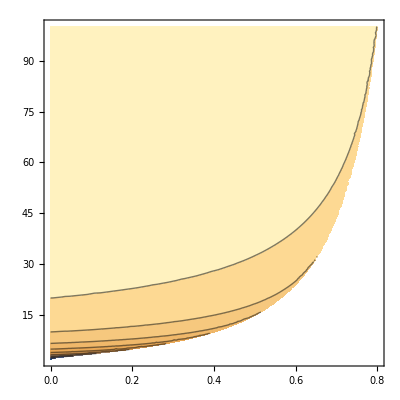

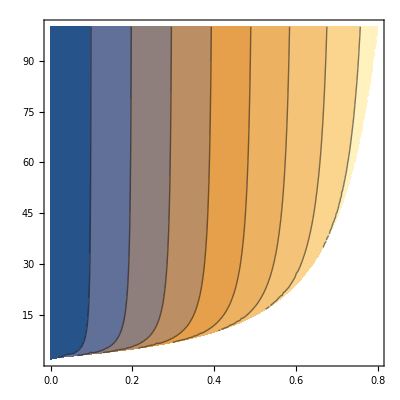

```mathematica
ContourPlot[(-2+d+√(4+d (-4+d (-1+μ)^2))+d μ)/(2 d),{μ,0,1},{d,2,100},PlotRange->All]
ContourPlot[(-2+d-√(4+d (-4+d (-1+μ)^2))+d μ)/(2 d),{μ,0,1},{d,2,100},PlotRange->All]
```

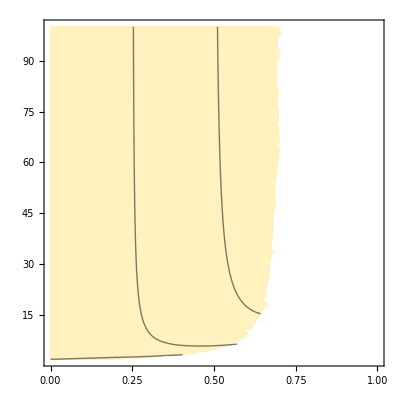

```mathematica
ContourPlot[((2+d (-1+m)) m)/(1+d (-1+m)),{m,0,1},{d,2,100}]
```

## WF

### Derivatives

```mathematica
bWFI=βWFI/.{Qin->QinWF,Qout->QoutWF}/.mychange//FullSimplify
bWF=βWFD-βWFI/.{Qin->QinWF,Qout->QoutWF}/.mychange//FullSimplify
cWF=γWFD-γWFI/.{Qin->QinWF,Qout->QoutWF}/.mychange//FullSimplify
combined = b bWF - c cWF//FullSimplify
```

((-1+μ) ((2+d (-2+m)) m-2 (1+d (-1+m))^2 μ+(1+d (-1+m))^2 μ^2))/((-1+d)^2 (-2+μ) μ (-1+(-1+n) (-2+μ) μ)-2 (-1+d) m (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ)+d m^2 (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ))

((-2+μ) (-1+μ) μ ((2+d (-2+m)) m-2 (1+d (-1+m))^2 μ+(1+d (-1+m))^2 μ^2))/((-1+d)^2 (-2+μ) μ (-1+(-1+n) (-2+μ) μ)-2 (-1+d) m (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ)+d m^2 (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ))

-((-2+μ) (-1+μ) μ ((2+d (-2+m)) m (-1+d n)-2 (1+d (-1+m))^2 (-1+n) μ+(1+d (-1+m))^2 (-1+n) μ^2))/((-1+d)^2 (-2+μ) μ (-1+(-1+n) (-2+μ) μ)-2 (-1+d) m (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ)+d m^2 (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ))

((-2+μ) (-1+μ) μ ((2+d (-2+m)) m (b+c (-1+d n))-2 (1+d (-1+m))^2 (b+c (-1+n)) μ+(1+d (-1+m))^2 (b+c (-1+n)) μ^2))/((-1+d)^2 (-2+μ) μ (-1+(-1+n) (-2+μ) μ)-2 (-1+d) m (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ)+d m^2 (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ))

```mathematica
dbi=D[bWFI,m]//FullSimplify
db=D[bWF,m]//FullSimplify
dc=D[cWF,m]//FullSimplify
```

-(2 (-1+d)^3 (1+d (-1+m)) n (-2+μ)^2 (-1+μ) μ^2)/(((-1+d)^2 (-2+μ) μ (-1+(-1+n) (-2+μ) μ)-2 (-1+d) m (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ)+d m^2 (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ))^2)

-(2 (-1+d)^3 (1+d (-1+m)) n (-2+μ)^3 (-1+μ) μ^3)/(((-1+d)^2 (-2+μ) μ (-1+(-1+n) (-2+μ) μ)-2 (-1+d) m (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ)+d m^2 (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ))^2)

(2 (-1+d)^3 (1+d (-1+m)) n (-2+μ)^2 (-1+μ) μ^2)/(((-1+d)^2 (-2+μ) μ (-1+(-1+n) (-2+μ) μ)-2 (-1+d) m (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ)+d m^2 (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ))^2)

```mathematica
Solve[dbi==0]//FullSimplify
sol=Solve[dbi==0,m]//FullSimplify
```

{{d→1},{m→(-1+d)/d},{n→0},{μ→0},{μ→1},{μ→2}}

{{m→(-1+d)/d}}

```mathematica
mc = (-1+d)/d;
```

```mathematica
sol/.{d->40,μ->0.01,n->4}
```

{{m→-1.13952},{m→0.77065}}

```mathematica
Plot[dbi/.{d->40,μ->0.01,n->4},{m,0,1}]
```

-Graphics-

```mathematica
mc=((-1+d) d (-1+μ) μ (1+(-1+n) μ)+√((-1+d)^2 d (-1+μ)^2 μ (n+(-1+μ)^2+d n^2 μ-n μ^2)))/(d (-1+μ)^2 (1+d (-1+n) μ));
```

```mathematica
D[mc,d]//FullSimplify
```

$Aborted

```mathematica
Solve[db==0]//FullSimplify
ss=Solve[db==0,m]//FullSimplify
```

{{n→((-1+μ) (-d m^2+(1+d (-1+m))^2 μ))/(μ (2 μ+d (-d m^2+2 (-2+m) μ+d (2+(-2+m) m) μ)))},{μ→0},{μ→1},{d→2/(1+√(-(-2+μ) μ)),m→1/2 (μ-√(-(-2+μ) μ))},{d→(2 (1+√(-(-2+μ) μ)))/(-1+μ)^2,m→1/2 (μ+√(-(-2+μ) μ))},{d→0,μ→0},{m→(-1+d)/d,μ→1}}

{{m→((-1+d) d (-1+μ) μ (1+(-1+n) μ)+√(-(-1+d)^2 d (-1+μ)^2 μ (-1+μ (2-μ+n (2 (-1+μ)+d (-1+(-1+n) (-2+μ) μ))))))/(d (-1+μ)^2 (1+d (-1+n) μ))},{m→((-1+d) d (-1+μ) μ (1+(-1+n) μ)-√(-(-1+d)^2 d (-1+μ)^2 μ (-1+μ (2-μ+n (2 (-1+μ)+d (-1+(-1+n) (-2+μ) μ))))))/(d (-1+μ)^2 (1+d (-1+n) μ))}}

```mathematica
ss/.{d->30,n->4}
```

```mathematica
ContourPlot[(-2+d+√(4+d (-4+d (-1+μ)^2))+d μ)/(2 d),{μ,0,1},{d,2,100},PlotRange->All]
ContourPlot[(-2+d-√(4+d (-4+d (-1+μ)^2))+d μ)/(2 d),{μ,0,1},{d,2,100},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
ContourPlot[((2+d (-1+m)) m)/(1+d (-1+m)),{m,0,1},{d,2,100}]
```

-Graphics-

```mathematica
dcb=D[combined,m]//FullSimplify
Solve[dcb==0]
```

-(2 (-1+d)^3 (1+d (-1+m)) n (-2+μ)^2 (-1+μ) μ^2 (c+b (-2+μ) μ))/(((-1+d)^2 (-2+μ) μ (-1+(-1+n) (-2+μ) μ)-2 (-1+d) m (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ)+d m^2 (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ))^2)

{{c→2 b μ-b μ^2},{d→1},{m→(-1+d)/d},{n→0},{μ→0},{μ→1},{μ→2}}

```mathematica
Limit[(1/μ dcb),μ->0]
```

0

```mathematica
ddcb=D[dcb,m]//FullSimplify
```

(2 (-1+d)^3 n (-2+μ)^2 (-1+μ) μ^2 (c+b (-2+μ) μ) (4 (1+d (-1+m))^2 (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ)-d ((-1+d)^2 (-2+μ) μ (-1+(-1+n) (-2+μ) μ)-2 (-1+d) m (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ)+d m^2 (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ))))/((-1+d)^2 (-2+μ) μ (-1+(-1+n) (-2+μ) μ)-2 (-1+d) m (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ)+d m^2 (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ))^3

```mathematica
minmax=ddcb/.{m->(-1+d)/d}//FullSimplify
```

-(2 d^3 n (-2+μ)^2 (-1+μ) μ^2 (c+b (-2+μ) μ))/((-1+d) (-1+(-1+d n) (-2+μ) μ)^2)

```mathematica
Solve[minmax==0,μ]//FullSimplify
```

{{μ→0},{μ→0},{μ→1},{μ→2},{μ→2},{μ→1-(√(b (b-c)))/b},{μ→(b+√(b (b-c)))/b}}

```mathematica
1-(√(b (b-c)))/b-(1-√(1-c/b))/.{b->2,c->1}
```

0

```mathematica
tmp=minmax/.{d->30,n->4,b->3,c->1}
tmp/.μ->0.0001
tmp/.μ->0.9
```

-(216000 (-2+μ)^2 (-1+μ) μ^2 (1+3 (-2+μ) μ))/(29 (-1+119 (-2+μ) μ)^2)

0.000284014

-0.101879

$Aborted

## Identity by descent

### Moran

#### In

```mathematica
qinm=QinM/.mychange//FullSimplify
```

-((-1+μ) (μ-d μ+m (-1+d μ)))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))

```mathematica
qinms=((1-μ) (m+μ(d(1-m)-1)))/((d-1) μ (1+(n-1) μ)+m (1-μ) (1+d (n-1) μ));
```

```mathematica
qinms-qinm//FullSimplify
```

0

```mathematica
Collect[Denominator[qinms],μ,FullSimplify]
```

m+(-1+d-m+d m (-1+n)) μ+(-1+d-d m) (-1+n) μ^2

#### Out

```mathematica
qoutm=QoutM/.mychange//FullSimplify
```

(m (-1+μ))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))

```mathematica
qoutms=(m (1-μ))/((d-1) μ (1+(n-1) μ)+m (1-μ) (1+d (n-1) μ));
```

```mathematica
qoutms-qoutm//FullSimplify
```

0

#### Plot

{d→4,n→4,μ→0.1}

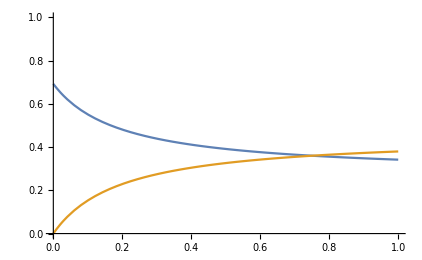

```mathematica
prs={d->4,n->4,μ->0.1}
Plot[{qinm/.prs,qoutm/.prs},{m,0,1},PlotRange->{0,1}]
```

{d→4,n→4,μ→0.1}

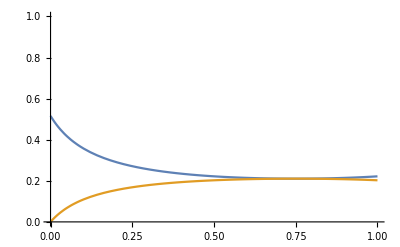

```mathematica
prs={d->4,n->4,μ->0.1}
Plot[{qinwfs/.prs,qoutwfs/.prs},{m,0,1},PlotRange->{0,1}]
```

```mathematica
LogLinearPlot[βBD/.{Qin->QinM,Qout->QoutM}/.mychange/.{n->4,μ->0.1,m->0.1,p->0.45},{d,4,10000000},PlotRange->All]
```

-Graphics-

### WF

#### In

```mathematica
qinwf=QinWF/.mychange//FullSimplify
```

(-d+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/(d (-1+n)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))

```mathematica
M1=(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2);
M2=1/(2 μ-μ^2);
```

```mathematica
qinwfs=(-d + M1+M2)/((n-1)d+M1+M2);
```

```mathematica
qinwf-qinwfs//FullSimplify
```

0

```mathematica
M1
```

(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)

```mathematica
M1s=(d-1)/(1-((d (1-m)-1)^2 (1-μ)^2)/(d-1)^2);
M1-M1s//FullSimplify
```

0

```mathematica
Limit[QinWF,μ->0]
Limit[qinwf,μ->0]
```

1

1

```mathematica
Limit[QinWF,d->∞]
Limit[qinwf,d->∞]//FullSimplify
```

((din^2-2 din dself+dself^2-(-1+m)^2) (-1+μ)^2)/(-1+2 m-m^2-2 m n+m^2 n+din^2 (-1+μ)^2-2 din dself (-1+μ)^2+dself^2 (-1+μ)^2+2 μ-4 m μ+2 m^2 μ-2 n μ+4 m n μ-2 m^2 n μ-μ^2+2 m μ^2-m^2 μ^2+n μ^2-2 m n μ^2+m^2 n μ^2)

-((-1+m)^2 (-1+μ)^2)/(-1-2 m (-1+n) (-1+μ)^2+m^2 (-1+n) (-1+μ)^2+(-1+n) (-2+μ) μ)

#### Out

```mathematica
qoutwf=QoutWF/.mychange//FullSimplify
```

(-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/(d (-1+n)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))

```mathematica
qoutwfs=(-1/(d-1)M1+M2)/(d(n-1)+M1+M2)//FullSimplify
```

(-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/(d (-1+n)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))

```mathematica
qoutwfs-qoutwf//FullSimplify
```

0

```mathematica
ExportForR[x_]:=Module[{xx},xx=x/.{μ->mu,d->ndemes};xx]
```

```mathematica
ExportForR[qinm]
```

-((-1+mu) (mu-mu ndemes+m (-1+mu ndemes)))/(-mu (1+mu (-1+n)) (-1+ndemes)+m (-1+mu) (1+mu (-1+n) ndemes))

## Export to R

#### Export to R the Q results

Rewrite the Greek letters

```mathematica
GreekTerms={ω->sel, μ->mut}
```

{ω→sel,μ→mut}

Common parts to all functions

```mathematica
FunctionPartB=" <- function(p, sel, mut, m, g, n, d, Idself, Ieself){
## Arguments:
#  p   mutation bias
#  sel intensity of selection
#  mut mutation probability
#  m   emigration probability
#  g   proportion of interactions out of the group (interaction equivalent of m)
#  n   deme size
#  d   number of demes
#  Idself whether reproduction in site where the parent is
#  Ieself whether interactions with oneself
return(
";
FunctionPartE=")
}";
```

Function to translate Mathematica to R

```mathematica
ToRForm[x_]:=ToString[x/.GreekTerms//CForm]
```

Do it for Q

```mathematica
RtxtQinM="QinM "<>FunctionPartB<>ToRForm[QinM/.genericde//FullSimplify]<>FunctionPartE;
RtxtQoutM="QoutM "<>FunctionPartB<>ToRForm[QoutM/.genericde//FullSimplify]<>FunctionPartE;
RtxtQinWF="QinWF "<>FunctionPartB<>ToRForm[QinWF/.genericde//FullSimplify]<>FunctionPartE;
RtxtQoutWF="QoutWF "<>FunctionPartB<>ToRForm[QoutWF/.genericde//FullSimplify]<>FunctionPartE;
```

Define Power function in R

```mathematica
PowerDef="Power <- function(a,b) return(a^b)";
```

Combine all texts

```mathematica
Rtxt=PowerDef<>"

"<>RtxtQinM<>"

"<>RtxtQoutM<>"

"<>RtxtQinWF<>"

"<>RtxtQoutWF;
```

Export to txt file (Mathematica did not want R)

```mathematica
Export["Documents/Work/Projects/2016_SocEvolSubdivPop/Programs/Mathematica/analyticsQ.txt",Rtxt]
```

Documents/Work/Projects/2016_SocEvolSubdivPop/Programs/Mathematica/analyticsQ.txt

Convert the file extension to R

```mathematica
<<"!mv Documents/Work/Projects/2016_SocEvolSubdivPop/Programs/Mathematica/analyticsQ.txt Documents/Work/Projects/2016_SocEvolSubdivPop/Programs/Mathematica/analyticsQ.R"
```

#### Export to R the β and γ functions

Rewrite the Greek letters

```mathematica
GreekTerms={ω->sel, μ->mut}
```

{ω→sel,μ→mut}

Common parts to all functions

```mathematica
FunctionPartB=" <- function(p, sel, mut, m, g, n, d, Idself, Ieself){
## Arguments:
#  p   mutation bias
#  sel intensity of selection
#  mut mutation probability
#  m   emigration probability
#  g   proportion of interactions out of the group (interaction equivalent of m)
#  n   deme size
#  d   number of demes
#  Idself whether reproduction in site where the parent is
#  Ieself whether interactions with oneself
return(
";
FunctionPartE=")
}";
```

Function to translate Mathematica to R

```mathematica
ToRForm[x_]:=ToString[x/.GreekTerms//CForm]
```

Do it for β and γ

```mathematica
RtxtbBDD="bBDD "<>FunctionPartB<>ToRForm[βBDD/.{Qin->QinM,Qout->QoutM}/.genericde//FullSimplify]<>FunctionPartE;
RtxtbBDI="bBDI "<>FunctionPartB<>ToRForm[βBDI/.{Qin->QinM,Qout->QoutM}/.genericde//FullSimplify]<>FunctionPartE;
RtxtcBDD="cBDD "<>FunctionPartB<>ToRForm[γBDD/.{Qin->QinM,Qout->QoutM}/.genericde//FullSimplify]<>FunctionPartE;
RtxtcBDI="cBDI "<>FunctionPartB<>ToRForm[γBDI/.{Qin->QinM,Qout->QoutM}/.genericde//FullSimplify]<>FunctionPartE;
```

```mathematica
RtxtbDBD="bDBD "<>FunctionPartB<>ToRForm[βDBD/.{Qin->QinM,Qout->QoutM}/.genericde//FullSimplify]<>FunctionPartE;
RtxtbDBI="bDBI "<>FunctionPartB<>ToRForm[βDBI/.{Qin->QinM,Qout->QoutM}/.genericde//FullSimplify]<>FunctionPartE;
RtxtcDBD="cDBD "<>FunctionPartB<>ToRForm[γDBD/.{Qin->QinM,Qout->QoutM}/.genericde//FullSimplify]<>FunctionPartE;
RtxtcDBI="cDBI "<>FunctionPartB<>ToRForm[γDBI/.{Qin->QinM,Qout->QoutM}/.genericde//FullSimplify]<>FunctionPartE;
```

```mathematica
RtxtbWFD="bWFD "<>FunctionPartB<>ToRForm[βWFD/.{Qin->QinWF,Qout->QoutWF}/.genericde//Simplify]<>FunctionPartE;
RtxtbWFI="bWFI "<>FunctionPartB<>ToRForm[βWFI/.{Qin->QinWF,Qout->QoutWF}/.genericde//Simplify]<>FunctionPartE;
RtxtcWFD="cWFD "<>FunctionPartB<>ToRForm[γWFD/.{Qin->QinWF,Qout->QoutWF}/.genericde//Simplify]<>FunctionPartE;
```

```mathematica
RtxtcWFI="cWFI "<>FunctionPartB<>ToRForm[γWFI/.{Qin->QinWF,Qout->QoutWF}/.genericde//Simplify]<>FunctionPartE;
```

Define Power function in R

```mathematica
PowerDef="Power <- function(a,b) return(a^b)";
```

Combine all texts

```mathematica
Rtxt=PowerDef<>"

"<>RtxtbBDD<>"

"<>RtxtbBDI<>"

"<>RtxtcBDD<>"

"<>RtxtcBDI<>"

"<>RtxtbDBD<>"

"<>RtxtbDBI<>"

"<>RtxtcDBD<>"

"<>RtxtcDBI<>"

"<>RtxtbWFD<>"

"<>RtxtbWFI<>"

"<>RtxtcWFD<>"

"<>RtxtcWFI;
```

Export to txt file (Mathematica did not want R)

```mathematica
Export["Documents/Work/Projects/2016_SocEvolSubdivPop/Programs/Mathematica/analyticsBC.txt",Rtxt]
```

Documents/Work/Projects/2016_SocEvolSubdivPop/Programs/Mathematica/analyticsBC.txt

Convert the file extension to R

```mathematica
<<"!mv Documents/Work/Projects/2016_SocEvolSubdivPop/Programs/Mathematica/analyticsBC.txt Documents/Work/Projects/2016_SocEvolSubdivPop/Programs/Mathematica/analyticsBC.R"
```

## Test

```mathematica
tmp=(-d+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/(d (-1+n)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))//Factor
FullSimplify[Numerator[tmp]]
FullSimplify[Denominator[tmp]]
```

-(((-1+μ)^2 (2 m-2 d m+d m^2-2 μ+4 d μ-2 d^2 μ-4 d m μ+4 d^2 m μ-2 d^2 m^2 μ+μ^2-2 d μ^2+d^2 μ^2+2 d m μ^2-2 d^2 m μ^2+d^2 m^2 μ^2))/(-2 m+2 d m-d m^2+2 μ-4 d μ+2 d^2 μ+4 m μ-4 d^2 m μ+2 d m^2 μ+2 d^2 m^2 μ-4 d m n μ+4 d^2 m n μ-2 d^2 m^2 n μ-5 μ^2+10 d μ^2-5 d^2 μ^2-2 m μ^2-8 d m μ^2+10 d^2 m μ^2-d m^2 μ^2-5 d^2 m^2 μ^2+4 n μ^2-8 d n μ^2+4 d^2 n μ^2+10 d m n μ^2-10 d^2 m n μ^2+5 d^2 m^2 n μ^2+4 μ^3-8 d μ^3+4 d^2 μ^3+8 d m μ^3-8 d^2 m μ^3+4 d^2 m^2 μ^3-4 n μ^3+8 d n μ^3-4 d^2 n μ^3-8 d m n μ^3+8 d^2 m n μ^3-4 d^2 m^2 n μ^3-μ^4+2 d μ^4-d^2 μ^4-2 d m μ^4+2 d^2 m μ^4-d^2 m^2 μ^4+n μ^4-2 d n μ^4+d^2 n μ^4+2 d m n μ^4-2 d^2 m n μ^4+d^2 m^2 n μ^4))

-(-1+μ)^2 ((2+d (-2+m)) m-2 (1+d (-1+m))^2 μ+(1+d (-1+m))^2 μ^2)

(-1+d)^2 (-2+μ) μ (-1+(-1+n) (-2+μ) μ)-2 (-1+d) m (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ)+d m^2 (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ)

```mathematica
FullSimplify[tmp/.μ->1-nμ]
```

-(nμ^2 (-(-1+d) (-1+d (-1+m)^2+2 m)+(1+d (-1+m))^2 nμ^2))/((-1+d) (-1+d (-1+m)^2+2 m) nμ^2-(1+d (-1+m))^2 nμ^4+n (-1+nμ^2) (-(-1+d)^2+(1+d (-1+m))^2 nμ^2))

```mathematica
QinM
```

((-1+μ) ((-1+d) (1+din-dself) μ+m (1+din-dself-(d+din-dself) μ)))/(m (-1+μ) (1+din-dself+(-din+dself+d (-1+n)) μ)+(-1+d) μ (-1+dself+din (-1+μ)+μ-(dself+n) μ))

```mathematica
Collect[tmp//FullSimplify,μ,FullSimplify]
```

-((-1+μ)^2 ((2+d (-2+m)) m-2 (1+d (-1+m))^2 μ+(1+d (-1+m))^2 μ^2))/((-1+d)^2 (-2+μ) μ (-1+(-1+n) (-2+μ) μ)-2 (-1+d) m (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ)+d m^2 (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ))

```mathematica
tmp//FullSimplify
```

-((-1+μ)^2 ((2+d (-2+m)) m-2 (1+d (-1+m))^2 μ+(1+d (-1+m))^2 μ^2))/((-1+d)^2 (-2+μ) μ (-1+(-1+n) (-2+μ) μ)-2 (-1+d) m (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ)+d m^2 (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ))

```mathematica
Collect[Numerator[tmp], μ,FullSimplify]
```

-(2+d (-2+m)) m+2 (1+2 m+d (-2+d (-1+m)^2+m^2)) μ+(-5-2 m-d (-10+5 d (-1+m)^2+m (8+m))) μ^2+4 (1+d (-1+m))^2 μ^3-(1+d (-1+m))^2 μ^4

### Derivatives

#### Moran

```mathematica
D[qinms,m]//FullSimplify
Solve[%==0]
```

((-1+d)^2 n (-1+μ) μ^2)/((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))^2

{{d→1},{n→0},{μ→0},{μ→1}}

```mathematica
D[qoutms,m]//FullSimplify
Solve[%==0]
```

-((-1+d) (-1+μ) μ (1+(-1+n) μ))/((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))^2

{{d→1},{n→(-1+μ)/μ},{μ→0},{μ→1}}

#### WF

```mathematica
qinwfs
```

(-d+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/(d (-1+n)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))

```mathematica
1/(1-(1-μ)^2)-M2//Simplify
```

0

```mathematica
sols=Solve[qinwfs==0]//FullSimplify
```

{{m→(-1+d-2 (-1+d) d μ+(-1+d) d μ^2-√((-1+d)^2 (1+d (-2+μ) μ)))/(d (1+d (-2+μ) μ))},{m→(-1+d-2 (-1+d) d μ+(-1+d) d μ^2+√((-1+d)^2 (1+d (-2+μ) μ)))/(d (1+d (-2+μ) μ))},{μ→1},{d→0,m→-1/2 (-2+μ) μ}}

```mathematica
sols/.{d->10,μ->0.001}
```

{{m→-0.00913265},{m→1.80913},{0.001→1},{10→0,m→0.0009995}}

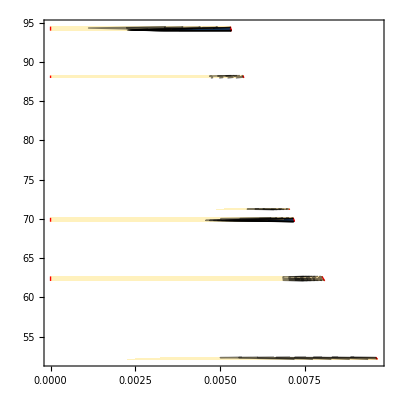

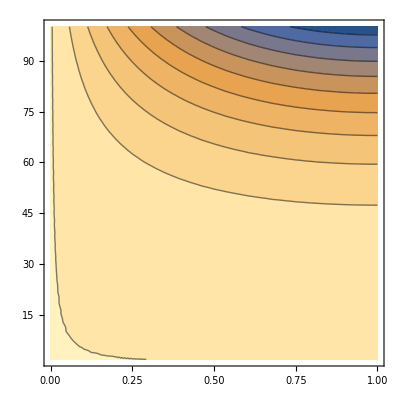

```mathematica
ContourPlot[(-1+d-2 (-1+d) d μ+(-1+d) d μ^2-√((-1+d)^2 (1+d (-2+μ) μ)))/(d (1+d (-2+μ) μ)),{μ,0,1},{d,2,100},PlotRange->All,RegionFunction->Function[{x,y,z},(-1+y)^2 (1+y (-2+x) x)>0],BoundaryStyle->Red]
ContourPlot[(-1+d)^2 (1+d (-2+μ) μ),{μ,0,1},{d,2,100},PlotRange->All]
```

```mathematica
qoutwfs
```

(-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/(d (-1+n)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))

```mathematica
Solve[qoutwfs==0]
```

{{m→0},{m→(2 (-1+d))/d},{μ→1}}

```mathematica
M1-((d-1)/(1-((d (1-m)-1)^2 (1-μ)^2)/(d-1)^2))//FullSimplify
```

0

```mathematica
M1//Factor//FullSimplify
```

-(-1+d)^3/((-2+d (2+m (-1+μ)-μ)+μ) (-d m+μ+d (-1+m) μ))

```mathematica
D[qinwfs,m]//FullSimplify
Solve[%==0]
```

(2 (-1+d)^3 (1+d (-1+m)) n (-2+μ)^2 (-1+μ)^2 μ^2)/(((-1+d)^2 (-2+μ) μ (-1+(-1+n) (-2+μ) μ)-2 (-1+d) m (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ)+d m^2 (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ))^2)

{{d→1},{m→(-1+d)/d},{n→0},{μ→0},{μ→1},{μ→2}}

```mathematica
D[qoutwfs,m]//FullSimplify
Solve[%==0]
```

-(2 (-1+d)^2 (1+d (-1+m)) (-2+μ) (-1+μ)^2 μ (-1+(-1+n) (-2+μ) μ))/(((-1+d)^2 (-2+μ) μ (-1+(-1+n) (-2+μ) μ)-2 (-1+d) m (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ)+d m^2 (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ))^2)

{{d→1},{m→(-1+d)/d},{n→(-1+μ)^2/((-2+μ) μ)},{μ→0},{μ→1},{μ→2}}

```mathematica
Solve[(1+d (-1+m))==0,m]
```

{{m→(-1+d)/d}}

```mathematica
Limit[qoutwfs,μ->0]
Limit[qinwfs,μ->0]
```

1

1

```mathematica
Limit[qoutwfs,d->∞]
Limit[qinwfs,d->∞]//FullSimplify
Limit[%,μ->0]//FullSimplify
1/n+(n-1)/n%//FullSimplify
```

0

-((-1+m)^2 (-1+μ)^2)/(-1-2 m (-1+n) (-1+μ)^2+m^2 (-1+n) (-1+μ)^2+(-1+n) (-2+μ) μ)

-(-1+m)^2/(-1+(-2+m) m (-1+n))

-1/(-1+(-2+m) m (-1+n))

```mathematica
-(-1+m)^2/(-1+(-2+m) m (-1+n))-((1-m)^2/(1+(2-m) m (n-1)))//FullSimplify
```

0

```mathematica
Limit[qinms,d->∞]//FullSimplify
Limit[%,μ->0]//FullSimplify
1/n+(n-1)/n%//FullSimplify
```

(-1+m+μ-m μ)/(-1+m (-1+n) (-1+μ)+μ-n μ)

(-1+m)/(-1+m-m n)

1/(1+m (-1+n))

```mathematica
(-1+m)/(-1+m-m n)-((1-m)/(1+m (n-1)))//Simplify
```

0

#### Limits

```mathematica
BD=((-1+p) p ((-1+Qin-n Qin+n Qout) μ-d (-1+Qin+m (1+(-1+n) Qin-n Qout)+n (-Qin+Qout) μ)))/(d n μ)/.mychange/.{Qin->qinms,Qout->qoutms}//FullSimplify
```

-((-1+p) p (μ+d^2 (-1+m) (-2+μ) μ+d (m+(-3+μ) μ)))/(d (-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ)))

```mathematica
Limit[BD,d->∞]//FullSimplify
Limit[%,μ->0]//FullSimplify
```

-((-1+m) (-1+p) p (-2+μ))/(-1+m (-1+n) (-1+μ)+μ-n μ)

-(2 (-1+m) (-1+p) p)/(1+m (-1+n))